# Functions and the Map command

Math 250 - Mathematical Computing
Christopher Hanusa

## 5.1 Aim

In this tutorial, we learn how to apply functions to every element in a list and how to create our own function definitions.

## 5.2 Key function: Map

An extremely important function in Mathematica is  Map.  In other computer languages people use For loops to repeat the same set of rules multiple times.  In Mathematica we can often avoid using For loops entirely by using the Map command instead.

The Map command takes in two inputs: a function and a list.
Map applies the function to each entry of the list, returning the results in a new list.

For example, if you want to know the values of sin(x) for multiples of π/6, you can create the list of multiples of π/6 and then Map the Sin function onto the list:

```mathematica
Table[Sin[i],{i,0,2Pi,Pi/6}]
```

{0,1/2,(√3)/2,1,(√3)/2,1/2,0,-1/2,-(√3)/2,-1,-(√3)/2,-1/2,0}

```mathematica
piList=Range[0,2Pi,Pi/6]
```

{0,π/6,π/3,π/2,(2 π)/3,(5 π)/6,π,(7 π)/6,(4 π)/3,(3 π)/2,(5 π)/3,(11 π)/6,2 π}

```mathematica
Map[Sin,piList]
```

{0,1/2,(√3)/2,1,(√3)/2,1/2,0,-1/2,-(√3)/2,-1,-(√3)/2,-1/2,0}

More generically, if your list is {a,b,c} and your function is f, then Map will return a list with f evaluated at each entry:

```mathematica
Map[f,{a,b,c}]
```

{f[a],f[b],f[c]}

### Shorthand: /@

Because it is used so frequently, there is a shorthand for Map that you may see “out in the wild”.  It is the pair of symbols “Slash-At”: /@

```mathematica
Sin/@piList
```

{0,1/2,(√3)/2,1,(√3)/2,1/2,0,-1/2,-(√3)/2,-1,-(√3)/2,-1/2,0}

```mathematica
f/@{a,b,c}
```

{f[a],f[b],f[c]}

As before, you do not have to use the /@ operator.  You should first work to be comfortable how Map works and eventually you may find it useful.

### Examples

Example 5.2.1. Use Map and Range to define the following list as the variable triangle.

```mathematica
{{1},
{1,2},
{1,2,3},
{1,2,3,4},
{1,2,3,4,5},
{1,2,3,4,5,6},
{1,2,3,4,5,6,7},
{1,2,3,4,5,6,7,8},
{1,2,3,4,5,6,7,8,9},
{1,2,3,4,5,6,7,8,9,10}}
```

```mathematica
Range[10]
```

{1,2,3,4,5,6,7,8,9,10}

```mathematica
triangle=Map[Range,Range[10]]
```

{{1},{1,2},{1,2,3},{1,2,3,4},{1,2,3,4,5},{1,2,3,4,5,6},{1,2,3,4,5,6,7},{1,2,3,4,5,6,7,8},{1,2,3,4,5,6,7,8,9},{1,2,3,4,5,6,7,8,9,10}}

```mathematica
{{1},
{1,2},
{1,2,3},
{1,2,3,4},
{1,2,3,4,5},
{1,2,3,4,5,6},
{1,2,3,4,5,6,7},
{1,2,3,4,5,6,7,8},
{1,2,3,4,5,6,7,8,9},
{1,2,3,4,5,6,7,8,9,10}}
```

Example 5.2.2. What is the difference between Length@triangle and Length/@triangle?

```mathematica
Length@triangle
```

10

```mathematica
Length/@triangle
```

{1,2,3,4,5,6,7,8,9,10}

Example 5.2.3. Use a Map command to find the sums of the entries in each list of triangle.

```mathematica
Map[Total,triangle]
```

{1,3,6,10,15,21,28,36,45,55}

## 5.3 Defining a named function

f[x_,y_] := RHS

(RHS stands for Right Hand Side.)

f is the coder-specified name of the function.  Since all built-in Mathematica functions start with a capital letter, it’s good practice to start user-defined functions with a lower case letter.  To use multiple-word function names, capitalize it #likeAHashtag.

All functions use square brackets [ ] to mark the beginning and end of the inputs.

Inside the square brackets, you give coder-specified names to each of the variables since you will be using them on the Right Hand Side of the definition when you code what the function does.

When you define these variables, use an underscore _ to tell Mathematica that the input for this variable can be any one thing. (One number, One list, One shape, ... anything!)  This is the simplest type of a “pattern” in Mathematica.

Unlike defining variables and using the = operator, when you define a function you use the := operator.  It is called “SetDelayed” because it means that every time you evaluate the left hand side (When you call the function), it RE-evaluates the Right Hand Side.  (See below for more information.)

### Simple function example

Define a function that takes as an input a number and outputs its square.

```mathematica
squareMe[x_]:=x^2
```

```mathematica
squareMe[-6]
```

36

Notice that Mathematica colors the coder-defined variables in the definition teal. If you had made a mistake and forgotten to include the underscore, the color would be different:

```mathematica
squareMe[x]:=x^2
```

### Simple function with more than one variable

Define a function that takes as an input two numbers and outputs its sum.

```mathematica
addEmUp[x_,y_]:=x+y
```

```mathematica
addEmUp[3,-10]
```

-7

```mathematica
Total[3,-10]
```

3

Notice that we did not specify that x and y had to be numbers.  Mathematica will add together whatever you put as inputs, even if the sum can’t be simplified.

```mathematica
addEmUp[{2,3},{9,-10}]
```

{11,-7}

```mathematica
addEmUp[Red,Orange]
```

RGBColor[1, 0, 0]+RGBColor[1, 0.5, 0]

```mathematica
addEmUp["Hello","Goodbye"]
```

Goodbye+Hello

### Examples

Example 5.3.1.  Define a function that takes as input a number and outputs that number plus a random integer between -5 and 5.

```mathematica
randomNoise[n_]:=n+RandomInteger[{-5,5}]
```

```mathematica
randomNoise[100]
```

105

Example 5.3.2. Take the function you defined in Example 5.3.1, apply it to all the elements in the list {1,...,100}, and create a scatterplot of the result.

```mathematica
Map[randomNoise,Range[100]]
```

{-4,-3,-1,4,8,9,8,7,6,13,12,13,9,18,15,18,22,21,15,20,20,27,25,19,22,30,25,32,31,35,33,32,37,37,30,38,35,43,40,38,41,38,44,40,43,45,42,43,45,45,55,53,50,56,55,56,57,54,64,61,57,60,63,65,66,69,70,73,64,67,66,73,75,71,71,75,74,83,82,78,80,85,83,83,87,89,92,86,91,87,90,90,89,89,98,96,99,103,98,99}

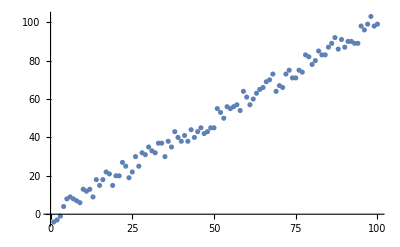

```mathematica
ListPlot[%]
```

Example 5.3.3. Modify the randomNoise function to allow for a second variable that defines how much noise to add.

```mathematica
randomNoise[n_,noise_]:=n+RandomInteger[{-noise,noise}]
```

```mathematica
randomNoise[100,100]
```

143

## 5.4 More information: Set vs. SetDelayed

Compare the following two lines of code:

```mathematica
x1=RandomInteger[{1,10}];
x2:=RandomInteger[{1,10}];
```

Notice that x1 is defined using Set (=) and x2 is defined using SetDelayed (:=).  This means that each time x1 is called, it will give the same random integer between 1 and 10, while each time x2 is called, it will give a new random integer between 1 and 10.

```mathematica
Table[x1,{10}]
```

{1,1,1,1,1,1,1,1,1,1}

```mathematica
Table[x2,{10}]
```

{2,3,4,4,1,7,3,2,6,5}

## 5.5 Nest and NestList

Another instance where computer languages often use a For loop involves applying the same function over and over to an initial input.  
In Mathematica, use the Nest command instead.  
And if you want to see the intermediate results, use the NestList command.

```mathematica
?Nest
?NestList
```

RowBox[{"Nest", "[", RowBox[{StyleBox["f", "TI"], ",", StyleBox["expr", "TI"], ",", StyleBox["n", "TI"]}], "]"}] gives an expression with StyleBox["f", "TI"] applied StyleBox["n", "TI"] times to StyleBox["expr", "TI"].

NestList[f,expr,n] gives a list of the results of applying f to expr 0 through n times.

Here is an example that uses the function “subtract one”, and applies it to the input 100 four times in a row.  When you do this, you get the final answer 96, because
subtractOne[subtractOne[subtractOne[subtractOne[100]]]]=((((100-1)-1)-1)-1)=96.

```mathematica
subtractOne[x_]:=x-1
Nest[subtractOne,100,4]
```

96

But perhaps you wanted to know all the intermediate results.  Then use NestList to see the initial input, and the four steps.

```mathematica
NestList[subtractOne,100,4]
```

{100,99,98,97,96}

## 5.6 An advanced extension: MapThread

Map is used to apply a function (that takes one input) to each element in a list of objects.

When your function takes multiple inputs, and you want more than one of those inputs to vary, you need to use MapThread instead.

### Syntax

Suppose your function takes in three inputs, x, y, and z:

```mathematica
function[x_,y_,z_]:=x^2+y^2+z^2
```

And you have a list of x-values, a list of y-values, and a list of z-values, ALL OF THE SAME LENGTH!

```mathematica
xlist=Range[10]
ylist=RandomInteger[{1,10},10]
zlist=Range[10,1,-1]
```

{1,2,3,4,5,6,7,8,9,10}

{8,1,4,9,1,1,7,8,10,5}

{10,9,8,7,6,5,4,3,2,1}

Then to evaluate the function with the first input in each list, then the second input in each list, then the third input in each list, etcetera, use MapThread.  
MapThread takes two inputs:  the first input is the function that will be applied and the second input is a list of the input lists.  (Read that again to make sure you understand what it is saying.)

Here is the continuation of the above example, in which we use MapThread to calculate f(x_1,y_1,z_1) then f(x_2,y_2,z_2) then f(x_3,y_3,z_3) through f(x_10,y_10,z_10).

```mathematica
MapThread[function,{xlist,ylist,zlist}]
```

{165,86,89,146,62,62,114,137,185,126}

This is equivalent to the following more complex code:

```mathematica
Table[function[xlist[[i]],ylist[[i]],zlist[[i]]],{i,1,Length[xlist]}]
```

### Examples

Example 5.6.1.  Calculate Sin[0], Cos[Pi/3], Tan[2Pi/3], Cot[Pi], Sec[4Pi/3] and Csc[5Pi/3] using MapThread.

```mathematica
flist={Sin,Cos,Tan,Cot,Sec,Csc};
values=Range[0,5Pi/3,Pi/3]
```

{0,π/3,(2 π)/3,π,(4 π)/3,(5 π)/3}

```mathematica
applyFunction[function_,value_]:=function[value]
```

```mathematica
MapThread[applyFunction,{flist,values}]
```

{0,1/2,-√3,ComplexInfinity,-2,-2/(√3)}

Example 5.6.2.  Create the following list of colorful days of the week.   (Hint: To add color or other font styling, use the Style function.)

{Monday,Tuesday,Wednesday,Thursday,Friday}

```mathematica
Style["Monday",Red]
```

Monday

```mathematica
daysOfWeek={"Monday","Tuesday","Wednesday","Thursday","Friday"};
colors={Red,Orange,Yellow,Green,Blue};
colorFunction[word_,color_]:=Style[word,color]
```

```mathematica
colorFunction["Monday",Red]
```

Monday

```mathematica
MapThread[colorFunction,{daysOfWeek,colors}]
```

{Monday,Tuesday,Wednesday,Thursday,Friday}